## Section | Matrix Quantum Mechanics

paul.c.abbott@uwa.edu.au

Ref: Computing quantum eigenvalues made easy Korsch and Glück (2002), Eur. J. Phys. 23 413-426

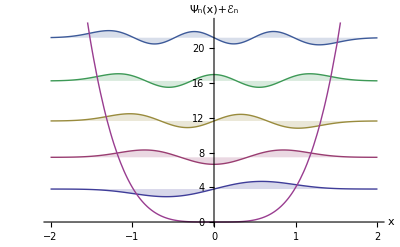

A fundamental problem in quantum mechanics is the calculation of the discrete spectrum of the Schrödinger operator. This question introduces a straightforward matrix method for computing the eigenvalues of operators. By expanding both the states of the system and the operators in a suitable basis set |ν⟩, ν=0,1,…, the problem is transformed into a matrix equation.

With a discrete matrix representation of the position, x_(μ,ν)=⟨μ|x̂|ν⟩, and momentum operators, p_(μ,ν)=⟨μ|p̂|ν⟩, in a convenient representation |ν⟩, μ,ν=0,1,2,…, one can use the (completeness of the) matrix representation to compute matrix elements of other operators, such as the potential ⟨μ|V̂(x̂)|ν⟩, the kinetic energy ⟨μ|T̂(p̂)|ν⟩, or a general operator ⟨μ|𝒪̂(x̂,p̂)|ν⟩.

### Harmonic oscillator eigenstates

In terms of normalized eigenstates of the harmonic oscillator Hamiltonian,

(Ĥ)_0=(p̂)^2/(2m)+1/2 m ω_0^2(x̂)^2,

the (infinite) matrix representation of the position operator, x̂, is

x=x_0/(√2)(0 | √1 | 0 | 0 | ⋯
√1 | 0 | √2 | 0 | ⋯
0 | √2 | 0 | √3 | ⋯
0 | 0 | √3 | 0 | ⋯
⋮ | ⋮ | ⋮ | ⋮ | ⋱),

where {x}_(μ,ν)≡x_(μ,ν)=⟨μ|x̂|ν⟩, and the matrix representation of the momentum operator, p̂,  is

p=(ⅈ p_0)/(√2)(0 | -√1 | 0 | 0 | ⋯
√1 | 0 | -√2 | 0 | ⋯
0 | √2 | 0 | -√3 | ⋯
0 | 0 | √3 | 0 | ⋯
⋮ | ⋮ | ⋮ | ⋮ | ⋱),

where {p}_(μ,ν)≡p_(μ,ν)=⟨μ|p̂|ν⟩ and x_0=(ℏ/(m ω_0))^(1/2) and p_0=(ℏ m ω_0)^(1/2).

### Exercise 1

The harmonic oscillator eigenfunctions in coordinate space are

```mathematica
Subscript[ψ, ν_](x_)=(√π a 2^ν ν!)^(-1/2) ⅇ^(-x^2/(2 a^2)) Subscript[H, ν](x/a);
```

Verify that the ψ_ν are orthonormal by computing ⟨μ|ν⟩:=∫_(-∞)^∞ Conjugate[ψ_μ(x)] ψ_ν(x)ⅆx for μ,ν=0,1,…,4. [3 Marks]

Assuming that a>0 assists in the computation of this and other integrals in this section.

#### Solution

The ψ_ν are orthonormal:

```mathematica
⟨μ_|ν_⟩:=⟨μ|ν⟩=Assuming[a>0,∫_(-∞)^∞ Conjugate[Subscript[ψ, μ](x)] Subscript[ψ, ν](x)ⅆx]
```

```mathematica
Table[⟨μ|ν⟩,{μ,0,4},{ν,0,4}]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

### Exercise 2

Visualize (ψ_ν(x))^2+ℰ_ν for the energy eigenvalues ℰ_ν=ν+1/2 for ν=0,1,…,6, together with the potential, 1/2 x^2, on one plot for a=1. [3 Marks]

#### Solution

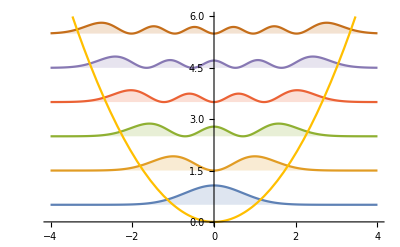

```mathematica
Plot[Evaluate[Append[Table[(Subscript[ψ, ν](x))^2+(ν+1/2)/.a->1,{ν,0,6}],1/2 x^2]],{x,-4,4},PlotRange->{0,6},Filling->Table[ν+1->ν+1/2,{ν,0,5}]]
```

### Exercise 3

Compute the discrete matrix representation of the position operator, x_(μ,ν)≡⟨μ|x̂|ν⟩:=∫_(-∞)^∞ Conjugate[ψ_μ(x)] x ψ_ν(x)ⅆx for μ,ν=0,1,…,4, and compare with equation (DisplayFormulaNumbered). [3 Marks]

#### Solution

⟨μ|x̂|ν⟩ agrees with equation (DisplayFormulaNumbered) with a=x_0.

```mathematica
⟨μ_ |x̂|ν_⟩:=Assuming[a>0,∫_(-∞)^∞ Conjugate[Subscript[ψ, μ](x)]x Subscript[ψ, ν](x)ⅆx]
```

```mathematica
(√2)/a Table[⟨μ |x̂|ν⟩,{μ,0,4},{ν,0,4}]
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

```mathematica
1/((√2)/a)/.a->Subscript[x, 0]
```

x_0/(√2)

### Exercise 4

In coordinate space, the momentum operator reads p̂=-ⅈ ℏ ∂_x. Compute the discrete matrix representation of the momentum operator, p_(μ,ν)=⟨μ|p̂|ν⟩=-ⅈ ℏ∫_(-∞)^∞ Conjugate[ψ_μ(x)] ∂_x ψ_ν(x)ⅆx for μ,ν=0,1,…,4,  and compare with equation (DisplayFormulaNumbered). [3 Marks]

#### Solution

⟨μ|p̂|ν⟩ agrees with equation (DisplayFormulaNumbered) with a=ℏ/p_0.

```mathematica
⟨μ_ |p̂|ν_⟩:=Assuming[a>0,∫_(-∞)^∞ Conjugate[Subscript[ψ, μ](x)](-ⅈ ℏ D[Subscript[ψ, ν](x), x])ⅆx]
```

```mathematica
(√2 a)/(ⅈ ℏ) Table[⟨μ |p̂|ν⟩,{μ,0,4},{ν,0,4}]
```

(0 | -1 | 0 | 0 | 0
1 | 0 | -√2 | 0 | 0
0 | √2 | 0 | -√3 | 0
0 | 0 | √3 | 0 | -2
0 | 0 | 0 | 2 | 0)

```mathematica
1/((√2 a)/(ⅈ ℏ))/.a->ℏ/Subscript[p, 0]
```

(ⅈ p_0)/(√2)

### Exercise 5

The harmonic oscillator eigenfunctions in momentum space read

```mathematica
Subscript[φ, ν_](p_)=ⅈ^-ν (√π 2^ν ν!/a)^(-1/2) ⅇ^(-p^2 a^2/2) Subscript[H, ν](a p);
```

Verify that φ_ν(p) is the (inverse) Fourier transform of ψ_ν(x) for ν=0,1,…,4. [2 Marks]

#### Solution

```mathematica
Table[Simplify[Subscript[φ, ν](p)==(Subscript[ℱ, x]^-1)[Subscript[ψ, ν](x)](p),a>0],{ν,0,4}]
```

{True,True,True,True,True}

### Exercise 6

Compute the discrete matrix representation of the momentum operator, p_(μ,ν)=⟨μ|p̂|ν⟩ for μ,ν=0,1,…,4, in momentum space and compare with equation (DisplayFormulaNumbered). [2 Marks]

#### Solution

⟨μ|p̂|ν⟩ agrees with equation (DisplayFormulaNumbered) with a=1/p_0.

```mathematica
⟨μ_ |p̂|ν_⟩:=Assuming[a>0,∫_(-∞)^∞ Conjugate[Subscript[φ, μ](p)]p Subscript[φ, ν](p)ⅆp]
```

```mathematica
(√2 a)/ⅈ Table[⟨μ |p̂|ν⟩,{μ,0,4},{ν,0,4}]
```

(0 | -1 | 0 | 0 | 0
1 | 0 | -√2 | 0 | 0
0 | √2 | 0 | -√3 | 0
0 | 0 | √3 | 0 | -2
0 | 0 | 0 | 2 | 0)

```mathematica
1/((√2 a)/ⅈ)/.a->1/Subscript[p, 0]
```

(ⅈ p_0)/(√2)

### Raising and lowering operators

In the following we will use units in which m=ℏ=ω_0=1. The harmonic oscillator Hamiltonian becomes

(Ĥ)_0=1/2(p̂)^2+1/2(x̂)^2.

Introducing matrix representations of the raising operator (𝒶̂)^†,

a^†=(0 | 0 | 0 | 0 | ⋯
√1 | 0 | 0 | 0 | ⋯
0 | √2 | 0 | 0 | ⋯
0 | 0 | √3 | 0 | ⋯
⋮ | ⋮ | ⋮ | ⋱ | ⋱),

and lowering operator â,

a=(0 | √1 | 0 | 0 | ⋯
0 | 0 | √2 | 0 | ⋯
0 | 0 | 0 | √3 | ⋯
0 | 0 | 0 | 0 | ⋱
⋮ | ⋮ | ⋮ | ⋮ | ⋱),

the matrix representation of the position operator, x̂, is

x=1/(√2)(a^†+a),

and the matrix representation of the momentum operator, p̂, is

p=ⅈ/(√2)(a^†-a).

### Exercise 7

Define k×k matrix representations of the raising and lowering operators. Verify that a^†.a — the so-called number operator — is a diagonal matrix with eigenvalues 0,1,2,…,k-1, for k=10. [4 Marks]

#### Solution

```mathematica
a/:Subscript[a, k_]:=SparseArray[{{i_,j_}/;j==i+1->√(j-1)},{k,k}]
```

```mathematica
Subscript[a, 10]//Normal
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ConjugateTranspose[(Subscript[a, 10])].Subscript[a, 10]//Normal
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9)

```mathematica
Eigenvalues[%]//Sort
```

{0,1,2,3,4,5,6,7,8,9}

### Energies of the harmonic and quartic oscillator

### Exercise 8

Use equations (DisplayFormulaNumbered) and  (DisplayFormulaNumbered) to define k×k matrix representations of the position operator, x̂, momentum operator, p̂, and the harmonic oscillator Hamiltonian, (Ĥ)_0=1/2(p̂)^2+1/2(x̂)^2. Determine the eigenvalues (energies) of the Hamiltonian matrix for k=10 and comment. (Hint: if the k×k matrix representation of the position operator is denoted x_k then (x̂)^2↔x_k.x_k and similarly for p̂. What do you expect for the harmonic oscillator energies?) [4 Marks]

#### Solution

```mathematica
x/:Subscript[x, k_]:=1/(√2)(ConjugateTranspose[(Subscript[a, k])]+Subscript[a, k])
```

```mathematica
p/:Subscript[p, k_]:=ⅈ/(√2)(ConjugateTranspose[(Subscript[a, k])]-Subscript[a, k])
```

```mathematica
ℋ/:Subscript[ℋ, k_]:=1/2 Subscript[p, k].Subscript[p, k]+1/2 Subscript[x, k].Subscript[x, k]
```

```mathematica
Subscript[ℋ, 10]//Normal
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 15/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/2)

The eigenvalues of this matrix are just its diagonal entries. The first k-1 eigenvalues are of the expected form, ℰ_n=(n+1/2) for n=0,1,…,k-2. The error in the last eigenvalue is due to matrix truncation.

### Exercise 9

Suitably modify the Hamiltonian matrix so as to determine approximate values for the 7 lowest energies of the quartic oscillator, (Ĥ)_0=1/2(p̂)^2+α/2(x̂)^4 with α=1. Display a graph of the computed energies as a function of matrix size k to show the convergence behaviour. [5 Marks]

#### Solution

```mathematica
ℋ/:Subscript[ℋ, k_,α_]:=1/2 Subscript[p, k].Subscript[p, k]+α/2 Subscript[x, k].Subscript[x, k].Subscript[x, k].Subscript[x, k]
```

```mathematica
Subscript[ℋ, 10,1]//Normal//Expand
```

(5/8 | 0 | 1/(√2) | 0 | (√(3/2))/2 | 0 | 0 | 0 | 0 | 0
0 | 21/8 | 0 | √6 | 0 | (√(15/2))/2 | 0 | 0 | 0 | 0
1/(√2) | 0 | 49/8 | 0 | 3 √3 | 0 | (3 √(5/2))/2 | 0 | 0 | 0
0 | √6 | 0 | 89/8 | 0 | 4 √5 | 0 | (√(105/2))/2 | 0 | 0
(√(3/2))/2 | 0 | 3 √3 | 0 | 141/8 | 0 | 5 √(15/2) | 0 | (√105)/2 | 0
0 | (√(15/2))/2 | 0 | 4 √5 | 0 | 205/8 | 0 | 3 √42 | 0 | (3 √21)/2
0 | 0 | (3 √(5/2))/2 | 0 | 5 √(15/2) | 0 | 281/8 | 0 | 7 √14 | 0
0 | 0 | 0 | (√(105/2))/2 | 0 | 3 √42 | 0 | 369/8 | 0 | 33/(√2)
0 | 0 | 0 | 0 | (√105)/2 | 0 | 7 √14 | 0 | 379/8 | 0
0 | 0 | 0 | 0 | 0 | (3 √21)/2 | 0 | 33/(√2) | 0 | 171/8)

```mathematica
Clear[λ]
```

```mathematica
λ/:Subscript[λ, k_]:=λ/:Subscript[λ, k]=Sort[Eigenvalues[N[Subscript[ℋ, k,1]]]]
```

```mathematica
λ/:Subscript[λ, k_,ν_]:=Subscript[λ, k]⟦ν+1⟧
```

```mathematica
ArrayFlatten[({{{{ν}}, {Table["k_(<>)="<>ToString[k],{k,10,50,10}]}}, {Table[{ν},{ν,0,6}], Table[Subscript[λ, k,ν],{ν,0,6},{k,10,50,10}]}})]
```

(ν | k_=10 | k_=20 | k_=30 | k_=40 | k_=50
0 | 0.529804 | 0.53018 | 0.530181 | 0.530181 | 0.530181
1 | 1.88438 | 1.8998 | 1.89984 | 1.89984 | 1.89984
2 | 3.70375 | 3.7277 | 3.72785 | 3.72785 | 3.72785
3 | 5.49767 | 5.82105 | 5.82235 | 5.82237 | 5.82237
4 | 7.09218 | 8.1372 | 8.13092 | 8.13091 | 8.13091
5 | 8.27486 | 10.6057 | 10.6195 | 10.6192 | 10.6192
6 | 22.1154 | 13.0881 | 13.2647 | 13.2643 | 13.2642)

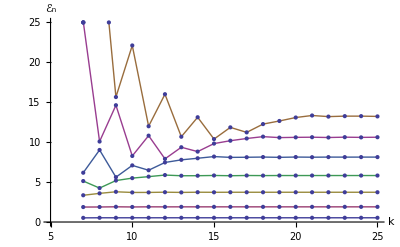

```mathematica
ListPlot[Table[{k,Subscript[λ, k,ν]},{ν,0,6},{k,7,25}],Joined->True,Mesh->All,PlotRange->{{5,Automatic},{0,25}},AxesOrigin->{5,0},AxesLabel->{k,Subscript[ℰ, n]}]
```

### Eigenfunctions

Denote the k eigenvectors of the k×k Hamiltonian matrix by c_n, n=0,1,…,k-1. Then one has the corresponding coordinate space wavefunction,

Ψ_n(x)=∑_(ν=0)^(k-1) c_(n,ν)ψ_ν(x),

and momentum space wavefunction,

Φ_n(p)=∑_(ν=0)^(k-1) c_(n,ν)φ_ν(p),

where c_(n,ν) is the ν^th component of the eigenvector c_n.

### Exercise 10

Compute the momentum space wavefunctions Φ_n(p) for the quartic oscillator with α=8, using matrices of size k=50. Plot the momentum distributions (‖Φ_ν(p)‖)^2≡Φ_ν(p)^*Φ_ν(p) for ν=0,1,…,5. [5 Marks]

#### Solution

```mathematica
Clear[λ,λc,c]
```

```mathematica
λc(k_):=λc(k)=Transpose[Sort[Transpose[Chop[Eigensystem[N[Subscript[ℋ, k,8]]]]]]]
```

```mathematica
λ/:Subscript[λ, k_,n_]:=λc(k)⟦1,n+1⟧
```

```mathematica
c/:Subscript[c, k_,n_]:=λc(k)⟦2,n+1⟧
```

```mathematica
Φ/:Subscript[Φ, k_,n_]:=p↦Evaluate[Subscript[c, k,n].Subscript[φ, Range[0,k-1]](p)/.a->1]
```

```mathematica
Ψ/:Subscript[Ψ, k_,n_]:=x↦Evaluate[Subscript[c, k,n].Subscript[ψ, Range[0,k-1]](x)/.a->1]
```

```mathematica
TabView@Table[n->Plot[Evaluate[Conjugate[Subscript[Φ, 60,n](p)]Subscript[Φ, 60,n](p)],{p,-10,10},PlotRange->{0,0.35},AxesLabel->{p,(‖Subscript[Φ, n](p)‖)^2}],{n,0,5}]
```

123456

Compare these to the corresponding coordinate space wavefunctions:

```mathematica
TabView@Table[n->Plot[Evaluate[Conjugate[Subscript[Ψ, 60,n](x)]Subscript[Ψ, 60,n](x)],{x,-2,2},PlotRange->{0,0.95},AxesLabel->{x,(‖Subscript[Ψ, n](x)‖)^2}],{n,0,5}]
```

123456

Also, it is revealing to plot Ψ_n(x) shifted upwards by the corresponding energy eigenvalue ℰ_n, superimposed on a plot of the potential V(x)=4 x^4.

```mathematica
Plot[Evaluate@Append[Table[Subscript[Ψ, 60,n](x)+Subscript[λ, 60,n],{n,1,5}],4 x^4],{x,-2,2},PlotRange->{0,23},AxesLabel->{x,Subscript[Ψ, n](x)+Subscript[ℰ, n]},Filling->Table[n->Subscript[λ, 60,n],{n,1,5}]]
```

-Graphics-

Note that the wavefunctions have an inflection point where they intersect the potential curve.

Exercises

1 + 2 + 3

To get to the next Exercise use Alt-2 or the pull down menu

No, you don’t need to write exercises either, particularly for monographs.

Q&A

Do I have to use a Q&A section?

No, but we do prefer it to internal breaks in your text.

Tech Notes

This is a useful section for data that breaks up the flow of your text. We prefer smaller Tech Notes sections in general

You can use it to provide additional data on your functions, that may have broken the narrative flow.

Example of TechNote Input/Output:

Plus[3928,5420]

9348

More to Explore

Use this section to include references to helpful links.  Have a leading line of text, and then provide a link.  We will make it a short-cite during the typesetting process.  Note that we prefer cross reference to other Wolfram materials, (Stephen Wolfram Blog, Wolfram Blog, Wolfram Functions, Wolfram DataRepository items, Wolfram Alpha, Wolfram Demonstrations, Mathworld, Wolfram Community, are all great resources with which to link.

Items in this section should resemble:

If you'd like to learn more about Programming with Built-in Computational Intelligence check out:  wolfr.am/language

References

Use Chicago Style in your reference section. We have provided this References section for those who prefer in chapter reference sections.  However, generally we preferences to be at the end of the book as a Bibliography.  For citations within chapters, please use standard (Author, Date) in-text citation.